```mathematica
Clear["Global`*"]
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=1/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
```

Let’s test our formulas:

```mathematica
Plot3D[ggx[Cos[x],y],{x,0,π/2},{y,0.001,1}]
Plot3D[smith[x,y],{x,0,π/2},{y,0.001,1},PlotRange->{0,2},AxesLabel->{"θ","α","Smith"}]
change[0,π/2,0]
```

-Graphics3D-

-Graphics3D-

1/(√2)

```mathematica
Manipulate[Plot3D[change[θo,θ,ϕ],{θ,0,π/2},{ϕ,-π,π},PlotRange->{0,1},AxesLabel->{"θ_i","ϕ_i","θ_h"}],{{θo,0},0,π/2}]
```

```mathematica
Clear[θ,α]
(* Makes no sense since smith is in macro space and ggx in half-vector space *)
(*Integrate[smith[θ,α]*ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Assumptions->{α>0,α<=1}]*)
```

1/(4 π α^4 (-1+α^2) √(-1+α^4))(-2 α^3 √(-1+α^4)+2 α^5 √(-1+α^4)-2 π √(-1+α^2) √(-1+α^4)+π α^2 √(-1+α^2) √(-1+α^4)+2 √(1+α^2) (2-3 α^2+α^4) ArcTan[1/(√(-1+α^2))]+2 (-1+α^2) √(-1+α^4) Log[(1-α)/(1+α)]+2 √(-1+α^4) Log[1-α^2]-2 α^2 √(-1+α^4) Log[1-α^2]-2 ⅈ √(1-α^2) Log[(-1+√(1+α^2))/(1+√(1+α^2))]+ⅈ α^2 √(1-α^2) Log[(-1+√(1+α^2))/(1+√(1+α^2))]+ⅈ α^4 √(1-α^2) Log[(-1+√(1+α^2))/(1+√(1+α^2))]-2 ⅈ √(1-α^2) Log[(α+√(1+α^2))/(-α+√(1+α^2))]+ⅈ α^2 √(1-α^2) Log[(α+√(1+α^2))/(-α+√(1+α^2))]+ⅈ α^4 √(1-α^2) Log[(α+√(1+α^2))/(-α+√(1+α^2))])

```mathematica
Clear[θi,ϕ,α]
(* This takes ages to complete and returns the stupid terms expansion below *)
(*Integrate[smith[θi,α]*ggx[change[θi,θo,ϕ],α]*Cos[θi]*Sin[θi],{θi,0,π/2},Assumptions->{α>0,α<=1,θo≥0,θo<π/2,ϕ>=-π,ϕ<=π}]*)
```

Integrate[(α^2 Cos[θi] Sin[θi])/(π (Cos[θi]+√(α^2+(1-α^2) Cos[θi]^2)) (1+(-1+α^2) Cos[(Cos[θi]+Cos[θo])/(√2 √(1+Cos[θi] Cos[θo]+Sin[θi] Sin[θo] Sin[ϕ]))]^2)^2),{θi,0,π/2},Assumptions→{α>0,α≤1,θo≥0,θo<π/2,ϕ≥-π,ϕ≤π}]

Here we verify that, ignoring Fresnel at the moment, whatever the roughness the total specular reflectance over the entire hemisphere is always 1:

```mathematica
Manipulate[2π*Integrate[ggx[Cos[θ],α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{{α,0.5},0.001,1}]
```

But if we make the masking/shadowing term intervene, then the integral is not 1 anymore as soon as the roughness != 0:
Actually, makes no sense since smith is in macro space while NDF is in half-vector space!

```mathematica
(*Manipulate[2π*Integrate[smith[θ,α]*ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{α,0.001,1}]*)
```

### Numerical Integration

Let’s try Mathematica’s numerical integration instead and see if we can go faster:

```mathematica
(* Don't evaluate that! Takes FOREVER! *)
(*Ei[θo_,ϕ_,α_]:=Integrate[smith[θi,α]*ggx[change[θo,θi,ϕ],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]*)
Ei[0,0,0.5]
```

$Aborted

```mathematica
Ei[θo_,ϕ_,α_]:=NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕ],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]
θo=0;
ϕ=0;
α=0.5;
Ei[0,0,0.5]
```

0.218949

Indeed it IS faster! :D

Technically, the expression we need to evaluate is this:

```mathematica
Eo[θo_,α_]:=smith[θo,α]*Integrate[Integrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}],{ϕi,-π,π}]
```

With numerical integration we instead get:

```mathematica
ϕi = -π;
θo=0.1;
α=0.5;
NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]
```

0.247075

```mathematica
θo=0.2;
α=0.005;
smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
(*smith[θo,α]*NIntegrate[Ei[θo,ϕi,α],{ϕi,-π,π}]*)
```

0.999974

Finally, we can build the final expression for irradiance:

```mathematica
Eo[θo_,α_]:=smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
Eo[0.1,0.5]
```

0.687578

So let’s build a table of these values!

```mathematica
countX = 128;
countY= 128;
buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=Max[0.01,y];
{x,y,N[Eo[θo,α]]}
]
buildTable[128*5+17]
```

Function[{i},x=N[Mod[i,countX]/(countX-1)];y=N[Quotient[i,countX]/(countY-1)];θo=ArcCos[x];α=Max[0.01,y];{x,y,N[Eo[θo,α]]}]

{0.133858,0.0393701,0.952105}

```mathematica
Manipulate[buildTable[i],{i,0,countX*countY-1,1}]
```

```mathematica
resultEo= Table[buildTable[i],{i,0,countX*countY-1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
ListPlot3D[resultEo]
Image[Table[Table[1-resultEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics3D-

-Graphics-

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
Export["MSBRDF_E128x128.csv",resultEo,"CSV"]
```

MSBRDF_E128x128.csv

```mathematica
testResultEo = Import["MSBRDF_E128x128.csv","CSV"];
ListPlot3D[testResultEo,AxesLabel->{"cos(θ)", "α","E_i"}]
```

-Graphics3D-

Let’s reorder the table and create an interpolation function from it:

```mathematica
t=Table[testResultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}];
fEo=ListInterpolation[t,{{0,1},{0,1}}]
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

-Graphics3D-

### Computing Average Irradiance

Now let’s integrate the full white furnace irradiance using our table:

	E_avg(α)=∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

```mathematica
resultEavg=Table[{N[i/(countY-1)],2*π*NIntegrate[fEo[μ,i/(countY-1)]μ,{μ,0,1}]},{i,0,countY-1}]
```

{{0.,3.13998},{0.00787402,3.13998},{0.015748,3.13794},{0.023622,3.13408},{0.0314961,3.12913},{0.0393701,3.12321},{0.0472441,3.1164},{0.0551181,3.10877},{0.0629921,3.10038},{0.0708661,3.09129},{0.0787402,3.08155},{0.0866142,3.07118},{0.0944882,3.06023},{0.102362,3.04874},{0.110236,3.03673},{0.11811,3.02424},{0.125984,3.01128},{0.133858,2.99789},{0.141732,2.98409},{0.149606,2.96991},{0.15748,2.95535},{0.165354,2.94045},{0.173228,2.92522},{0.181102,2.90967},{0.188976,2.89384},{0.19685,2.87773},{0.204724,2.86136},{0.212598,2.84474},{0.220472,2.82789},{0.228346,2.81083},{0.23622,2.79356},{0.244094,2.7761},{0.251969,2.75847},{0.259843,2.74066},{0.267717,2.72271},{0.275591,2.70461},{0.283465,2.68638},{0.291339,2.66802},{0.299213,2.64956},{0.307087,2.63099},{0.314961,2.61233},{0.322835,2.59359},{0.330709,2.57477},{0.338583,2.55589},{0.346457,2.53695},{0.354331,2.51796},{0.362205,2.49892},{0.370079,2.47985},{0.377953,2.46076},{0.385827,2.44164},{0.393701,2.42251},{0.401575,2.40337},{0.409449,2.38423},{0.417323,2.3651},{0.425197,2.34597},{0.433071,2.32687},{0.440945,2.30778},{0.448819,2.28872},{0.456693,2.26969},{0.464567,2.2507},{0.472441,2.23175},{0.480315,2.21285},{0.488189,2.194},{0.496063,2.1752},{0.503937,2.15646},{0.511811,2.13778},{0.519685,2.11917},{0.527559,2.10065},{0.535433,2.08216},{0.543307,2.06377},{0.551181,2.04545},{0.559055,2.02722},{0.566929,2.00908},{0.574803,1.99102},{0.582677,1.97305},{0.590551,1.95517},{0.598425,1.93739},{0.606299,1.91971},{0.614173,1.90213},{0.622047,1.88464},{0.629921,1.86726},{0.637795,1.84999},{0.645669,1.83282},{0.653543,1.81576},{0.661417,1.79882},{0.669291,1.78198},{0.677165,1.76525},{0.685039,1.74864},{0.692913,1.73215},{0.700787,1.71577},{0.708661,1.6995},{0.716535,1.68336},{0.724409,1.66733},{0.732283,1.65142},{0.740157,1.63564},{0.748031,1.61997},{0.755906,1.60443},{0.76378,1.589},{0.771654,1.5737},{0.779528,1.55852},{0.787402,1.54347},{0.795276,1.52853},{0.80315,1.51373},{0.811024,1.49904},{0.818898,1.48448},{0.826772,1.47004},{0.834646,1.45572},{0.84252,1.44153},{0.850394,1.42746},{0.858268,1.41352},{0.866142,1.3997},{0.874016,1.386},{0.88189,1.37242},{0.889764,1.35897},{0.897638,1.34564},{0.905512,1.33242},{0.913386,1.31934},{0.92126,1.30637},{0.929134,1.29352},{0.937008,1.28079},{0.944882,1.26818},{0.952756,1.2557},{0.96063,1.24333},{0.968504,1.23107},{0.976378,1.21894},{0.984252,1.20692},{0.992126,1.19502},{1.,1.18323}}

```mathematica
Export["MSBRDF_Eavg128.csv",resultEavg,"CSV"]
```

MSBRDF_Eavg128.csv

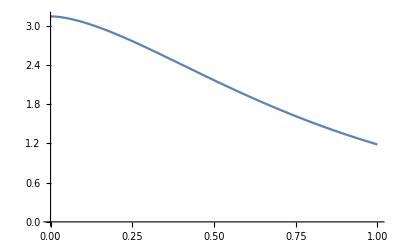

```mathematica
ListLinePlot[resultEavg]
```

InterpolatingFunction[{{0., 1.}}, <>]

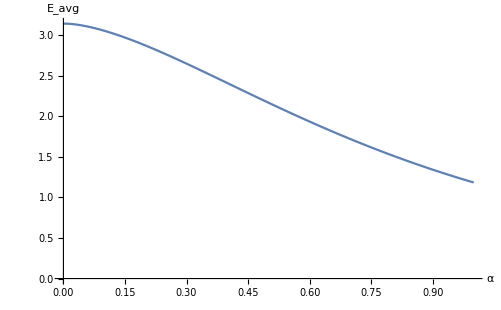

```mathematica
t=Table[resultEavg[[i]][[2]],{i,1,countY}];
fEavg=ListInterpolation[t,{0,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}]
```

Export as binary float arays for C#:

```mathematica
t=Table[testResultEo[[i]][[3]],{i,1,countX*countY}];
Export["MSBRDF_E128x128.float",t,"Real32"]
t=Table[resultEavg[[i]][[2]],{i,1,countY}];
Export["MSBRDF_Eavg128.float",t,"Real32"]
```

MSBRDF_E128x128.float

MSBRDF_Eavg128.float

## Let’s check the BRDFs sum to π!

```mathematica
BRDFggx[θo_,θi_,ϕ_,α_]:= smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α]
BRDFms[θo_,θi_,ϕ_,α_]:=((1-fEo[Cos[θo],α])*(1-fEo[Cos[θi],α]))/(π-fEavg[α])
```

```mathematica
whiteFurnace0[α_]:=2*π*NIntegrate[BRDFggx[θo,θi,ϕ,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace1[α_]:=2*π*NIntegrate[BRDFms[θo,θi,ϕ,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace[α_]:=2*π*NIntegrate[(BRDFggx[θo,θi,ϕ,α]+BRDFms[θo,θi,ϕ,α])*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

```mathematica
whiteFurnace0[0.3]
whiteFurnace1[0.3]
```

2.64771

0.493886

```mathematica
whiteFurnace[0.3]
```

3.14159

```mathematica
whiteFurnaceResult=Table[{α,whiteFurnace[Max[0.01,α]]},{α,0,1,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.500047 and 0.000053884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

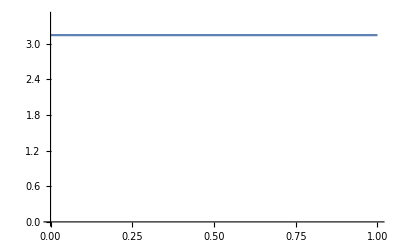

```mathematica
ListLinePlot[whiteFurnaceResult,PlotRange->{0,1.1*π}]
```

```mathematica
whiteFurnaceResult0=Table[{α,whiteFurnace0[Max[0.01,α]]},{α,0,1,0.05}]
whiteFurnaceResult1=Table[{α,whiteFurnace1[Max[0.01,α]]},{α,0,1,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.499733 and 0.0000510937 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.495579 and 1.18889×10^-6 for the integral and error estimates.

{{0.,3.13991},{0.05,3.11382},{0.1,3.05224},{0.15,2.96919},{0.2,2.87121},{0.25,2.76289},{0.3,2.64771},{0.35,2.52841},{0.4,2.4072},{0.45,2.28586},{0.5,2.16582},{0.55,2.0482},{0.6,1.93385},{0.65,1.82343},{0.7,1.7174},{0.75,1.61607},{0.8,1.51963},{0.85,1.42816},{0.9,1.34166},{0.95,1.26005},{1.,1.18323}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000314469 and 6.88027×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.,0.00197587},{0.05,0.0277751},{0.1,0.0893483},{0.15,0.172407},{0.2,0.270382},{0.25,0.378701},{0.3,0.493886},{0.35,0.613187},{0.4,0.734392},{0.45,0.855729},{0.5,0.975771},{0.55,1.0934},{0.6,1.20774},{0.65,1.31816},{0.7,1.42419},{0.75,1.52552},{0.8,1.62196},{0.85,1.71343},{0.9,1.79993},{0.95,1.88154},{1.,1.95836}}

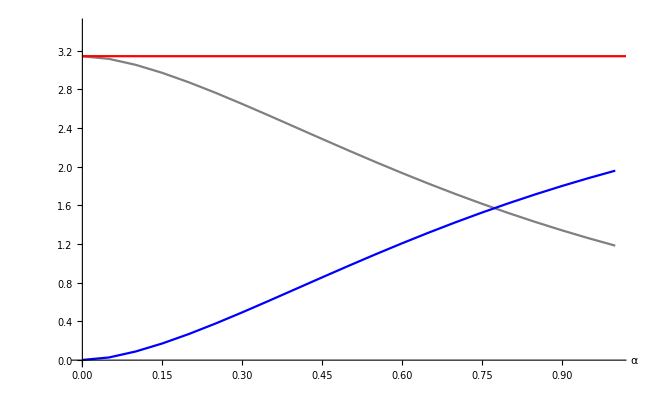

```mathematica
Show[
ListLinePlot[whiteFurnaceResult0,PlotRange->{0,1.1*π},PlotStyle->Gray,AxesLabel->{"α",""}],
ListLinePlot[whiteFurnaceResult1,PlotStyle->Blue],
ListLinePlot[whiteFurnaceResult0+whiteFurnaceResult1,PlotRange->Full,PlotStyle->Red]
]
```

### C# Simulation

```mathematica
(*SetDirectory[NotebookDirectory[]]; *)
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX = 32;
countY= 32;
rawFile=BinaryReadList["MSBRDF_E"<>ToString[countX]<>"x"<>ToString[countY]<>".float", "Real32"];
simulEo=Table[{Mod[i,countX]/(countX-1),Quotient[i,countX]/(countY-1), rawFile[[1+i]]},{i,0,countX*countY-1}];
```

```mathematica
ListPlot3D[simulEo,PlotRange->{0,1},AxesLabel->{"cos(θ)","α"}]
```

-Graphics3D-

```mathematica
Image[Table[Table[1-simulEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics-

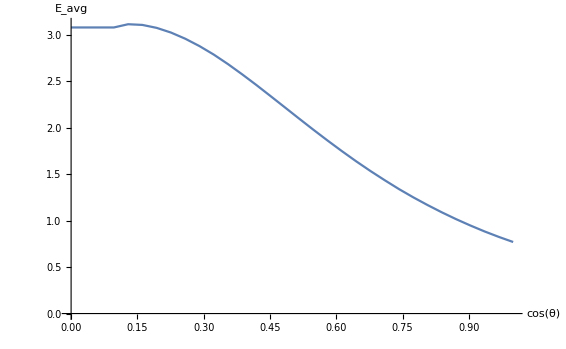

```mathematica
countX=32;
rawFileAvg=BinaryReadList["MSBRDF_Eavg32.float", "Real32"];
Eavg=Table[{Mod[i,countX]/(countX-1),rawFileAvg[[1+i]]},{i,0,countX-1}];
ListLinePlot[Eavg,AxesLabel->{"cos(θ)","E_avg"}]
```

### Importance Sampling of powers of cosine

```mathematica
Integrate[Cos[x]Sin[x],x]
```

-1/2 Cos[x]^2

```mathematica
D[Cos[x]^3,x]
```

-3 Cos[x]^2 Sin[x]